```mathematica
data=Map[ToExpression[#[[1]]]->ToExpression[#[[2]]]&,Import["/Users/ross/Dropbox/Research/MLearn/FACET.csv","Table"]];
```

```mathematica
(*data=ReleaseHold[Hold[Join[ToExpression["FACEINFO"],ToExpression["FACEINFO"]^2]->"FACETNREGTRIANG"]/.docs];
unknownData=ReleaseHold[Hold[Join[ToExpression["FACEINFO"],ToExpression["FACEINFO"]^2]]/.unknownDocs];*)
```

```mathematica
(*TrainInds=RandomSample[Range[Length[Data]],Floor[0.8*Length[Data]]];
TestInds=RandomSample[Complement[Range[Length[Data]],TrainInds]];*)
```

```mathematica
{TrainInds,TestInds}=GatherBy[Range[Length[data]],IntegerDigits[Hash[#,"SHA256"],256][[-1]]<(0.8*256)&];
```

```mathematica
methods={"LinearRegression","NearestNeighbors","NeuralNetwork","RandomForest","GaussianProcess"};
```

```mathematica
p=Predict[data[[TrainInds]],Method->"RandomForest"];
```

```mathematica
pm=PredictorMeasurements[p,data[[TestInds]]];
```

```mathematica
pm["StandardDeviation"]
```

1465.55

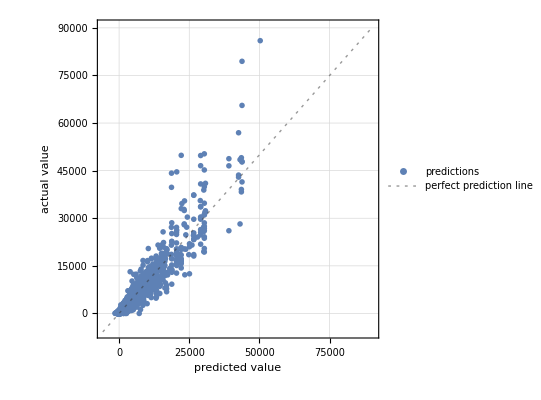

```mathematica
pm["ComparisonPlot"]
```

```mathematica
N[Count[Map[Abs[p[#[[1]]]-#[[2]]]<5&,data[[TestInds]]],True]/Length[TestInds]]*100
```

100.

```mathematica
PredictorInformation[p]
```

Predictor information
Method | K-nearest neighbors
Number of features | 9
Number of training examples | 48662
Number of neighbors | 10
Distance function | EuclideanDistance

```mathematica
net=NetChain[{LinearLayer[1000],
ElementwiseLayer[Ramp],
LinearLayer[10],
ElementwiseLayer[Ramp],
LinearLayer[100],
FlattenLayer[],
SummationLayer[]},"Input"->9];
```

```mathematica
net=NetTrain[net,data[[TrainInds]],MeanAbsoluteLossLayer[] ,ValidationSet->Scaled[0.2],MaxTrainingRounds->100];(*,TrainingProgressReporting->{"Print","Interval"->Quantity[1,"Rounds"]}];*)
```

```mathematica
N[Length[Select[Map[{Round[net[#[[1]]]],#[[2]]}&,data[[TrainInds]]],Abs[#[[1]]-#[[2]]]<5&]]/Length[TrainInds]]*100
```

3.7668

```mathematica
N[Length[Select[Map[{Round[net[#[[1]]]],#[[2]]}&,data[[TestInds]]],Abs[#[[1]]-#[[2]]]<5&]]/Length[TestInds]]*100
```

3.86598

```mathematica
N[Length[Select[Map[{Round[net[#[[1]]]],#[[2]]}&,data],Abs[#[[1]]-#[[2]]]<5&]]/Length[data]]*100
```

3.78646